# SEI2HR model with quarantine scenarios

## Version 0.4

Anton Antonov
MathematicaForPrediction at WordPress
SystemModeling at GitHub
March, April 2020

## Introduction

The model presented in this notebook -- SEI2HR --  deals with the left-most and middle rectangles in this diagram:

```mathematica
Import["https://github.com/antononcube/SystemModeling/raw/master/Projects/Coronavirus-propagation-dynamics/Diagrams/Coronavirus-propagation-simple-dynamics.jpeg"]
```

In this notebook we also deal with “quarantine scenarios”.

This graph shows the “big picture” of the model development plan undertaken in [AAr1]  and where the model discussed in this article is:

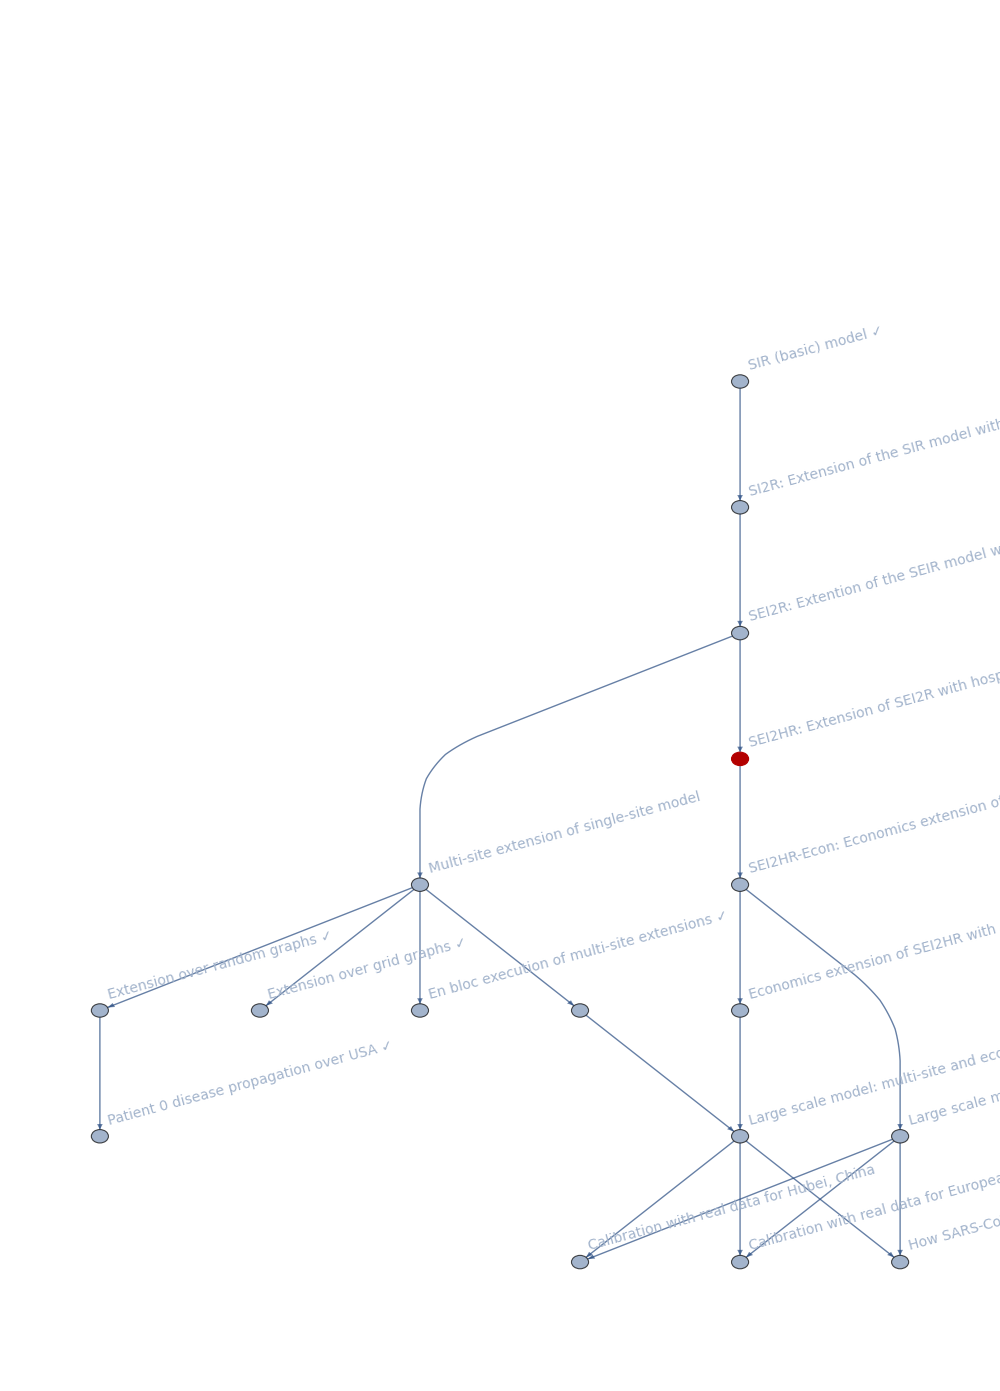

### The models

#### SEI2R

The model SEI2R are introduced and explained in the notebook [AA2]. SEI2R differs from the classical SEIR model , [Wk1, HH1], with the following elements:

1. Two separate infected populations: one is "severely symptomatic", the other is "normally symptomatic"

2. The monetary equivalent of lost productivity due to infected or died people is tracked.

Remark: We consider the coronavirus propagation models as instances of the more general System Dynamics (SD) models. We use SD terminology in this notebook.

#### SEI2HR

For the formulation of SEI2HR we use a system of Differential Algebraic Equations (DAE’s). The package [AAp1] allows for the use of non-algebraic formulation, that has just Ordinary Differential Equations (ODE’s).

### Notebook structure

The rest of notebook has the following sequence of sections:

Package load section

SEI2HR structure in comparison of SEI2R

Explanations of the equations of SEI2HR

Parameters and initial conditions setup

Populations, hospital beds, quarantine scenarios

Interactive interface

Sensitivity analysis

## Load packages

The epidemiological models framework used in this notebook is implemented with the packages [AAp1, AAp2, AA3]; the interactive plots functions are from the package [AAp4].

```mathematica
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModels.m"];Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelModifications.m"];Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelingVisualizationFunctions.m"];Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/WL/SystemDynamicsInteractiveInterfacesFunctions.m"],
```

## SEI2HR extends SEI2R

The model SEI2HR is an extension of SEI2R, [AA2]. Denote that extension with “SEI2R → SEI2HR”).

Here is SEI2R:

```mathematica
reprTP="AlgebraicEquation";
lsModelOpts={"Tooltips"->True,TooltipStyle->{Background->Yellow,CellFrameColor->Gray,FontSize->20}};
modelSEI2R=SEI2RModel[t,"InitialConditions"->True,"RateRules"->True,"TotalPopulationRepresentation"->reprTP];
ModelGridTableForm[modelSEI2R,lsModelOpts]
```

Here is SEI2HR:

```mathematica
modelSEI2HR=SEI2HRModel[t,"InitialConditions"->True,"RateRules"->True,"TotalPopulationRepresentation"->reprTP];
ModelGridTableForm[modelSEI2HR,lsModelOpts]
```

Here is the “difference” between the two models:

```mathematica
ModelGridTableForm@Merge[{modelSEI2HR,modelSEI2R},If[AssociationQ[#⟦1⟧],KeyComplement[#],Complement@@#]&]
```

## Equations explanations

In this section we provide rationale of the model equations of SEI2HR.

The equations for Susceptible, Exposed, Infected, Recovered populations of SEI2R are "standard" and explanations about them are found in [WK1, HH1]. For SEI2HR those equations change because of the stocks Hospitalized Population and Hospital Beds.

Remark: Note that the equations in section have tooltips for the stocks and rates (for more convenient reading.)

#### The infected and hospitalized populations

The SEI2HR has two types of infected populations: normally symptomatic one and a severely symptomatic one. A major assumption for SEI2R is that only the severely symptomatic people are hospitalized. (That assumption is also reflected in the diagram in the introduction.)

Each of those three populations have their own contact rates and mortality rates.

```mathematica
ColumnForm@Cases[Normal@modelSEI2HR["Rates"],HoldPattern[β[_]->_],∞]
```

```mathematica
ColumnForm@Cases[Normal@modelSEI2HR["Rates"],HoldPattern[μ[_]->_],∞]
```

Remark: Below with “Infected Population” we mean both stocks Infected Normally Symptomatic Population (INSP) and Infected Severely Symptomatic Population (ISSP).

#### Total Population

In this notebook we consider a DAE’s formulation of SEI2HR. The stock Total Population has the following (obvious) algebraic equation:

```mathematica
ModelGridTableForm[modelSEI2HR,lsModelOpts]["Equations"]⟦1,2,2⟧
```

We have used specified that the total population cannot be less than 0.

Remark: As mentioned in the introduction, the package [AAp1] allows for the use of non-algebraic formulation.

#### Susceptible Population

The stock Susceptible Population (SP) is decreased by (1) infections derived from stocks Infected Populations and Hospitalized Population (HP), and (2) morality cases derived with the typical mortality rate.

```mathematica
ModelGridTableForm[modelSEI2HR,lsModelOpts]["Equations"]⟦1,3,2⟧
```

Because we hospitalize the severely infected people only instead of the term

(ISSP[t]SP[t]β[ISSP])/TP[t]

we have the terms

(HP[t] SP[t] β[HP])/TP[t]+(Max[0,-HP[t]+ISSP[t]] SP[t] β[ISSP])/TP[t].

The first term is for the infections derived from the hospitalized population. The second term for the infections derived from people who infected and severely symptomatic and not hospitalized.

#### Exposed Population

The stock Exposed Population (EP) is increased by (1) infections derived from stocks Infected Populations and Hospitalized Population, and (2) morality cases derived with the typical mortality rate. EP is decreased by (1) the people who after a certain average incubation period (aincp) become ill, and (2) morality cases derived with the typical mortality rate.

```mathematica
ModelGridTableForm[modelSEI2HR,lsModelOpts]["Equations"]⟦1,4,2⟧
```

#### Infected Normally Symptomatic Population

INSP is increased by a fraction of the people who have been exposed. That fraction is derived from the severely symptomatic population fraction (sspf). INSP is decreased by (1) the people who recover after a certain average infection period (aip), and (2) the normally symptomatic people who die from the disease.

```mathematica
ModelGridTableForm[modelSEI2HR,lsModelOpts]["Equations"]⟦1,5,2⟧
```

#### Infected Severely Symptomatic Population

ISSP is increased by a fraction of the people who have been exposed. That fraction is the severely symptomatic population fraction (sspf). ISSP is decreased by (1) the people who recover after a certain average infection period (aip), (2) the hospitalized severely symptomatic people who die from the disease, and (3) the non-hospitalized severely symptomatic people who die from the disease.

```mathematica
ModelGridTableForm[modelSEI2HR,lsModelOpts]["Equations"]⟦1,6,2⟧
```

Note that we do not assume that severely symptomatic people recover faster if they are hospitalized, only that they have a different death rate.

#### Hospitalized Population

The amount of people that can be hospitalized is determined by the available Hospital Beds (HB) -- the stock Hospitalized Population (HP) is subject to a resource limitation by HB.

The equation of the stock HP can be easily understood from the following dynamics description points:

If the number of hospitalized people is less that the number of hospital beds we hospitalize the new ISSP people.

If the new ISSP people are more than the Available Hospital Beds (AHB) we take as many as AHB.

Hospitalized people have the same average infection period (aip).

Hospitalized (severely symptomatic) people have their own mortality rate.

```mathematica
ModelGridTableForm[modelSEI2HR,lsModelOpts]["Equations"]⟦1,7,2⟧
```

#### Recovered Population

The stock Recovered Population (RP) is increased by the recovered infected people and decreased by morality cases derived with the typical mortality rate.

```mathematica
ModelGridTableForm[modelSEI2HR,lsModelOpts]["Equations"]⟦1,8,2⟧
```

#### Deceased Infected Population

The stock Deceased Infected Population (DIP) accumulates the deaths of the people who are infected. Note that we utilize the different death rates for HP and ISSP.

```mathematica
ModelGridTableForm[modelSEI2HR,lsModelOpts]["Equations"]⟦1,9,2⟧
```

#### Hospital Beds

The stock Hospital Beds (HB) can change with a rate that reflects the number of hospital beds change rate (nhbcr) per day. Generally, using nhbcr we can capture scenarios, like, extending hospitals, building new hospitals, recruitment of new medical personnel, loss of medical personnel (due to infections.)

```mathematica
ModelGridTableForm[modelSEI2HR,lsModelOpts]["Equations"]⟦1,10,2⟧
```

#### Money for Hospital Services

The stock Money for Hospital Services (MHS) simply tracks expense for the hospitalized people.

```mathematica
ModelGridTableForm[modelSEI2HR,lsModelOpts]["Equations"]⟦1,11,2⟧
```

#### Money from Lost Productivity

The stock Money from Lost Productivity (MLP) simply tracks expense for the hospitalized people.

```mathematica
ModelGridTableForm[modelSEI2HR,lsModelOpts]["Equations"]⟦1,12,2⟧
```

## Parameters and actual simulation equations code

Here are the parameters we want to experiment with (or do calibration with):

```mathematica
lsFocusParams={aincp,aip,sspf[SP],β[HP],qsd,ql,qcrf,nhbcr[ISSP,INSP],nhbr[TP]};
aParametricRateRules=KeyDrop[modelSEI2HR["RateRules"],lsFocusParams];
```

Here we set custom rates and initial conditions:

```mathematica
population=10^6;
If[reprTP=="AlgebraicEquation",
modelSEI2HR=SetRateRules[modelSEI2HR,
<|
β[ISSP]->0.56*Piecewise[{{1,t<qsd},{qcrf,qsd≤t≤qsd+ql}},1],
β[INSP]->0.56*Piecewise[{{1,t<qsd},{qcrf,qsd≤t≤qsd+ql}},1],
qsd->60,
ql->8*7,
qcrf->0.25,
β[HP]->0.01,
μ[ISSP]->0.035/aip,
μ[INSP]->0.01/aip,
nhbr[TP]->population*3/1000,
lpcr[ISSP,INSP]->1,
hscr[ISSP,INSP]->1
|>];modelSEI2HR=SetInitialConditions[modelSEI2HR,<|TP[0]==population,SP[0]->population-1,ISSP[0]->0,INSP[0]->1|>],
(*ELSE*)
modelSEI2HR=SetRateRules[modelSEI2HR,<|TP[t]->population,β[ISSP]->0.56,β[INSP]->0.56,β[HP]->0.01,μ[ISSP]->0.035/aip,μ[INSP]->0.01/aip,μ[HP]->0.005/aip,nhbr[TP]->population*3/1000|>];modelSEI2HR=SetInitialConditions[modelSEI2HR,<|SP[0]->population-1,ISSP[0]->0,INSP[0]->1|>];
];
```

Here is the system of ODE’s we use to do parametrized simulations:

```mathematica
lsActualEquations=
Join[
modelSEI2HR["Equations"]//.KeyDrop[modelSEI2HR["RateRules"],lsFocusParams],
modelSEI2HR["InitialConditions"]//.KeyDrop[modelSEI2HR["RateRules"],lsFocusParams]
];
ResourceFunction["GridTableForm"][List/@lsActualEquations]
```

## Simulation

Straightforward simulation for one year using ParametricNDSolve :

```mathematica
aSol=
Association@Flatten@
ParametricNDSolve[lsActualEquations,GetStockSymbols[modelSEI2HR,__~~__],{t,0,365},lsFocusParams];
```

Example evaluation of a solution using parameters from the model object:

```mathematica
lsFocusParams//.modelSEI2HR["RateRules"]
```

```mathematica
With[{seq=Sequence@@(lsFocusParams//.modelSEI2HR["RateRules"]/.t->12)},aSol⟦2⟧[seq][12]]
```

## Interactive interface (quarantine)

```mathematica
opts={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->400};
lsPopulationKeys={TP,SP,EP,ISSP,INSP,HP,RP,DIP};
lsEconKeys={MHS,MMSP,MLP,DIP};
Manipulate[
DynamicModule[{lsPopulationPlots,lsEconPlots,lsRestPlots},

lsPopulationPlots=
ParametricSolutionsPlots[
modelSEI2HR["Stocks"],
KeyTake[aSol,lsPopulationKeys],
{aincp,aip,spf,crhp,qsd,ql,qcrf,nhbcr,nhbr/1000},ndays,
"LogPlot"->popLogPlotQ,"Together"->popTogetherQ,"Derivatives"->popDerivativesQ,"DerivativePrefix"->"Δ",opts];

lsEconPlots=
ParametricSolutionsPlots[
modelSEI2HR["Stocks"],
KeyTake[aSol,lsEconKeys],
{aincp,aip,spf,crhp,qsd,ql,qcrf,nhbcr,nhbr/1000},ndays,
"LogPlot"->econLogPlotQ,"Together"->econTogetherQ,"Derivatives"->econDerivativesQ,"DerivativePrefix"->"Δ",opts];

lsRestPlots=
ParametricSolutionsPlots[
modelSEI2HR["Stocks"],
KeyDrop[aSol,Join[lsPopulationKeys,lsEconKeys]],
{aincp,aip,spf,crhp,qsd,ql,qcrf,nhbcr,nhbr/1000},ndays,
"LogPlot"->econLogPlotQ,"Together"->econTogetherQ,"Derivatives"->econDerivativesQ,"DerivativePrefix"->"Δ",opts];

Multicolumn[Join[lsPopulationPlots,lsEconPlots,lsRestPlots],nPlotColumns,Dividers->All,FrameStyle->GrayLevel[0.8]]
],
{{aincp,6.,"Average incubation period (days)"},1,60.,1,Appearance->{"Open"}},
{{aip,21.,"Average infectious period (days)"},1,60.,1,Appearance->{"Open"}},
{{spf,0.2,"Severely symptomatic population fraction"},0,1,0.025,Appearance->{"Open"}},
{{qsd,60,"Quarantine start days"},0,365,0.01,Appearance->{"Open"}},
{{ql,8*7,"Quarantine length (in days)"},0,120,1,Appearance->{"Open"}},
{{qcrf,0.25,"Quarantine contact rate fraction"},0,1,0.01,Appearance->{"Open"}},
{{crhp,0.1,"Contact rate of the hospitalized population"},0,30,0.1,Appearance->{"Open"}},
{{nhbcr,0,"Number of hospital beds change rate"},-0.5,0.5,0.001,Appearance->{"Open"}},
{{nhbr,2.9,"Number of hospital beds rate (per 1000 people)"},0,100,0.1,Appearance->{"Open"}},
{{ndays,365,"Number of days"},1,365,1,Appearance->{"Open"}},
{{popTogetherQ,True,"Plot populations together"},{False,True}},
{{popDerivativesQ,False,"Plot populations derivatives"},{False,True}},
{{popLogPlotQ,False,"LogPlot populations"},{False,True}},
{{econTogetherQ,True,"Plot economics functions together"},{False,True}},
{{econDerivativesQ,False,"Plot economics functions derivatives"},{False,True}},
{{econLogPlotQ,True,"LogPlot economics functions"},{False,True}},
{{nPlotColumns,1,"Number of plot columns"},Range[5]},
ControlPlacement->Left,ContinuousAction->False]
```

## Sensitivity analysis

When making and using this kind of dynamics models it is important to see how the solutions react to changes of different parameters. I.e. what ranges of the which parameters bring dramatic changes into important stocks.

Remark: The sensitivity analysis shown below should be done for other stocks and rates. (In order to keep this exposition short it is not done here.)

### Definitions

```mathematica
Clear[VariabilityPlots];
Options[VariabilityPlots]=Options[Plot];
VariabilityPlots[aSol_Association,FOCUSSymbol_,parRange_,operation_String,opts:OptionsPattern[]]:=Block[{aincp=6.,aip=21.,crhp=0.1,econDerivativesQ=False,econLogPlotQ=False,econTogetherQ=False,ndays=365,nhbcr=0,nhbr=2.9,nPlotColumns=2,popDerivativesQ=False,popLogPlotQ=False,popTogetherQ=True,qcrf=0.25,ql=8*7,qsd=60,spf=0.2,funcs,funcPaths,plots},

plots=
Which[
operation=="Identity",
 prefix=Nothing;
funcs=Table[aSol[FOCUSSymbol][aincp,aip,spf,crhp,p,ql,qcrf,nhbcr,nhbr/1000][t],{p,parRange}];
funcPathEnds=Table[f/.t->ndays,{f,funcs}];
Plot[Evaluate@funcs,{t,0,ndays},Evaluate[opts],PlotLegends->parRange,ImageSize->Medium],

operation=="Derivative",
prefix="Δ";
funcs=Table[D[aSol[FOCUSSymbol][aincp,aip,spf,crhp,p,ql,qcrf,nhbcr,nhbr/1000][t],t],{p,parRange}];
funcPathEnds=Table[f/.t->ndays,{f,funcs}];
Plot[Evaluate@funcs,{t,0,ndays},Evaluate[opts],PlotLegends->parRange,ImageSize->Medium],

operation=="Integral",
prefix="∫";
funcs=Table[With[{pArg=p,fArg=aSol[FOCUSSymbol]},Function[{nd},NIntegrate[fArg[aincp,aip,spf,crhp,pArg,ql,qcrf,nhbcr,nhbr/1000][t],{t,0,nd},PrecisionGoal->3,AccuracyGoal->3,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]]],{p,parRange}];
funcPaths=Table[f[t],{f,funcs},{t,Union[Append[Range[0,ndays,10],ndays]]}];
funcPathEnds=Table[f[ndays],{f,funcs}];
ListLinePlot[funcPaths,Evaluate[opts],PlotLegends->parRange,ImageSize->Medium],

True,
Return[$Failed]
];

GridTableForm[
<|
Row[{prefix,FOCUSSymbol}]->plots,
Row[{"Differences at ",ndays}]->GridTableForm[List@@@Normal[AssociationThread[parRange,(First[#]-#&)@funcPathEnds]],TableHeadings->{"Parameter","Difference"}]
|>,
Background->White]
];
```

### Number of infected people

```mathematica
lsQStartRange=Union[Join[{365},Range[50,100,5],{140}]];
```

```mathematica
VariabilityPlots[aSol,ISSP,lsQStartRange,#,opts,ImageSize->300]&/@{"Identity","Integral"}
```

### Number of deceased people

```mathematica
VariabilityPlots[aSol,DIP,lsQStartRange,#,opts,ImageSize->300]&/@{"Identity","Derivative"}
```

### Number of hospitalized people

```mathematica
VariabilityPlots[aSol,HP,lsQStartRange,#,opts,ImageSize->300]&/@{"Identity","Integral"}
```

## References

### Articles

[Wk1] Wikipedia entry, "Compartmental models in epidemiology".

[HH1] Herbert W. Hethcote (2000). "The Mathematics of Infectious Diseases". SIAM Review. 42 (4): 599–653. Bibcode:2000SIAMR..42..599H. doi:10.1137/s0036144500371907.

[AA1] Anton Antonov, "Coronavirus propagation modeling considerations", (2020), SystemModeling at GitHub.

[AA2] Anton Antonov, "Basic experiments workflow for simple epidemiological models", (2020), SystemModeling at GitHub.

[AA3] Anton Antonov, "Scaling of Epidemiology Models with Multi-site Compartments", (2020), SystemModeling at GitHub.

### Repositories, packages

[WRI1] Wolfram Research, Inc., "Epidemic Data for Novel Coronavirus COVID-19", WolframCloud.

[AAr1] Anton Antonov, Coronavirus propagation dynamics project, (2020), SystemModeling at GitHub.

[AAp1] Anton Antonov, "Epidemiology models Mathematica package", (2020), SystemsModeling at GitHub.

[AAp2] Anton Antonov, "Epidemiology models modifications Mathematica package", (2020), SystemsModeling at GitHub.

[AAp3] Anton Antonov, "Epidemiology modeling visualization functions Mathematica package", (2020), SystemsModeling at GitHub.

[AAp4] Anton Antonov, "System dynamics interactive interfaces functions Mathematica package", (2020), SystemsModeling at GitHub.

### Project management files

[AAo1] Anton Antonov, WirVsVirus-Hackathon-work-plan.org, (2020), SystemsModeling at GitHub.

[AAo2] Anton Antonov, WirVsVirus-hackathon-Geo-spatial-temporal-model-mind-map, (2020), SystemsModeling at GitHub.